## 1D Symmetric

### Test

```mathematica
symClass=ChemDVRClass["Cartesian1DCsDVR"];
ChemDVRClear[symDVR];
symDVR=symClass[{100},{{-5, 5}}]
```

```mathematica
ChemDVRObject[…][]
```

```mathematica
Needs["ChemTools`DVR`"]
```

```mathematica
ChemDVRReload["SymmetricCartesian1DDVR"];
symClass=ChemDVRClass["SymmetricCartesian1DDVR"];
ChemDVRClear[symDVR];
symDVR=symClass[{100},{{-5, 5}}]
```

ChemDVRObject[…]

```mathematica
ke=symDVR[Return->"KineticEnergy"];
pe=symDVR[Return->"PotentialEnergy"];
```

```mathematica
wfns=symDVR[Return->"Wavefunctions"];
```

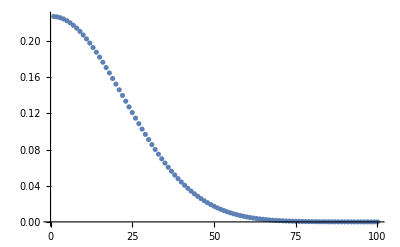
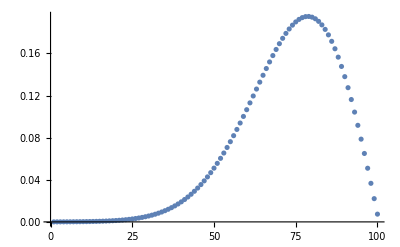
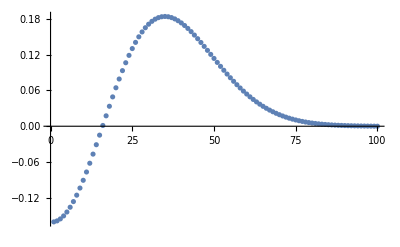

```mathematica
wfns[[2]]//Take[#, 3]&//Map[ListPlot]
```

```mathematica
symDVR[]
```

```mathematica
wfns[[1]]/wfns[[1,1]]
```

```mathematica
cartDVR[Return->"Wavefunctions"][[1]]
```

{0.357125,1.07138,1.78565,2.50011,3.21575,3.93641,4.67249,5.44312,6.27228,7.18079,8.18148,9.28011,10.4785,11.7768,13.1748,14.672,16.2679,17.9624,19.7551,21.6459,23.6346,25.7211,27.9052,30.187,32.5664,35.0432,37.6175,40.2893,43.0584,45.9249,48.8888,51.9501,55.1086,58.3646,61.7178,65.1683,68.7162,72.3613,76.1037,79.9435,83.8805,87.9148,92.0464,96.2753,100.601,105.025,109.546,114.164,118.879,123.691,128.601,133.608,138.713,143.914,149.213,154.61,160.103,165.694,171.382,177.168,183.05,189.031,195.108,201.283,207.554,213.924,220.39,226.954,233.615,240.374,247.229,254.183,261.233,268.381,275.626,282.968,290.408,297.945,305.579,313.311,321.14,329.067,337.089,345.211,353.428,361.745,370.156,378.668,387.273,395.979,404.778,413.68,422.671,431.769,440.951,450.246,459.616,469.114,478.734,487.494}

```mathematica
pe=symDVR[Return->"PotentialEnergy"];
```

```mathematica
symDVR[Function->Function[0]]
```

```mathematica
cartClass=ChemDVRClass["Cartesian1DDVR"];
cartDVR=cartClass[{100},{{-5,5}}]
```

ChemDVRObject[…]

```mathematica
wfns2=cartDVR[Return->"Wavefunctions"];
```

```mathematica
wfns2[[1]]/wfns2[[1,1]]
```

{1.,3.,5.00007,7.00067,9.00455,11.0225,13.0836,15.2415,17.5633,20.1072,22.9093,25.9856,29.3413,32.9768,36.8913,41.0836,45.5525,50.2973,55.3172,60.6117,66.1802,72.0227,78.1386,84.528,91.1904,98.126,105.334,112.816,120.57,128.596,136.896,145.468,154.312,163.429,172.819,182.481,192.415,202.622,213.101,223.853,234.877,246.174,257.743,269.584,281.698,294.085,306.743,319.674,332.878,346.354,360.102,374.122,388.415,402.981,417.819,432.929,448.312,463.967,479.895,496.095,512.567,529.312,546.329,563.62,581.182,599.017,617.124,635.504,654.155,673.081,692.277,711.748,731.489,751.505,771.791,792.352,813.183,834.289,855.665,877.316,899.236,921.433,943.898,966.64,989.649,1012.94,1036.49,1060.32,1084.42,1108.8,1133.44,1158.36,1183.54,1209.01,1234.73,1260.75,1286.99,1313.58,1340.52,1365.05}

```mathematica
wfns[[1]]/wfns[[1,1]]
```

{1.,1.,2.35532,2.35536,3.71284,3.71506,5.0511,5.09248,6.28546,6.56469,7.5819,8.26622,9.30778,10.2787,11.4443,12.6193,13.9333,15.2861,16.7549,18.2762,19.9017,21.5872,23.3701,25.2178,27.1584,29.167,31.2656,33.4344,35.6909,38.0194,40.434,42.9219,45.4946,48.1416,50.8725,53.6785,56.5674,59.5323,62.5794,65.7031,68.9084,72.1908,75.5542,78.9953,82.517,86.1166,89.7965,93.5548,97.3929,101.31,105.306,109.382,113.536,117.77,122.083,126.475,130.946,135.498,140.127,144.837,149.624,154.492,159.438,164.465,169.569,174.755,180.016,185.361,190.781,196.284,201.862,207.524,213.26,219.081,224.975,230.955,237.006,243.146,249.355,255.654,262.02,268.479,275.001,281.621,288.299,295.08,301.913,308.856,315.843,322.951,330.087,337.362,344.643,352.098,359.503,367.156,374.646,382.618,389.68,399.547}

### Cartesian1D Sanity Check

```mathematica
cartKE=cartDVR[Return->"KineticEnergy"];
cartPE=cartDVR[Return->"PotentialEnergy"];
```

```mathematica
transf2=
1/Sqrt[2]*With[{n=Length[cartKE]/2},
ArrayFlatten[{
{IdentityMatrix[n],Reverse/@IdentityMatrix[n]},
Reverse/@{IdentityMatrix[n],Reverse/@-IdentityMatrix[n]}
}]
];
```

```mathematica
realSoln=
ChemTools`Private`Hidden`ChemDVRDefaultWavefunctions[
transf2.cartKE.transf2,
cartPE
];
```

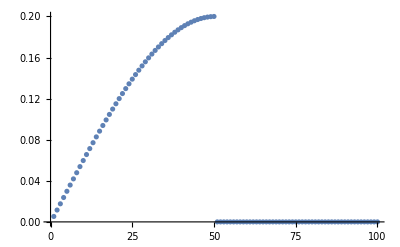
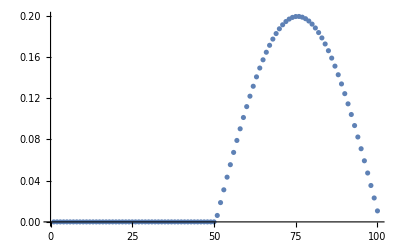
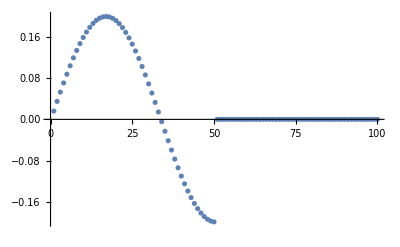

```mathematica
realSoln[[2]]//Take[#,3]&//Map[ListPlot]
```

### Transform

```mathematica
transf=
With[{n=2},
ArrayFlatten[{
{IdentityMatrix[n],Reverse/@IdentityMatrix[n]},
Reverse/@{IdentityMatrix[n],Reverse/@-IdentityMatrix[n]}
}]
];
```

```mathematica
torig=
Table[t[i,j],
{i,{2,1,-1,-2}},
{j,{2,1,-1,-2}}
]/.{
(t[i_,j_])/;(i<j):>t[-i,-j],
(t[i_?Positive,i_]):>t[-i,-i]
};
torig//MatrixForm
```

(t[-2,-2] | t[2,1] | t[2,-1] | t[2,-2]
t[-1,-2] | t[-1,-1] | t[1,-1] | t[1,-2]
t[1,-2] | t[1,-1] | t[-1,-1] | t[-1,-2]
t[2,-2] | t[2,-1] | t[2,1] | t[-2,-2])

```mathematica
tnew=
transf.torig.Inverse[transf]//FullSimplify;
tnew//MatrixForm
```

(t[-2,-2]+t[2,-2] | t[2,-1]+t[2,1] | 0 | 0
t[-1,-2]+t[1,-2] | t[-1,-1]+t[1,-1] | 0 | 0
0 | 0 | t[-1,-1]-t[1,-1] | t[-1,-2]-t[1,-2]
0 | 0 | -t[2,-1]+t[2,1] | t[-2,-2]-t[2,-2])

```mathematica
vecsorg=torig//Eigenvectors;
```

```mathematica
vecsnew=tnew//Eigenvectors;
```

```mathematica
vecsorg[[1,2]]
```

```mathematica
vecsnew[[1,1]]
```

## Symm DVR 2D

### Unsymm 2D Test

```mathematica
ChemDVRReload["Cartesian2DDVR"];
```

```mathematica
cartO=ChemDVRClass["Cartesian2DDVR"][{10,10}]
```

ChemDVRObject[…]

```mathematica
symmT2=
With[{n=10},
Array[
Which[
#==#2&&#≤n^2/2,1/(√2),
#==#2&&#>=n^2/2,-1/(√2),
#2==n^2-#+1,1/(√2),
True,0
]&,
{n^2,n^2}
]
];
```

```mathematica
cartK=cartO[Return->"KineticEnergy"];
```

```mathematica
k=symmT2.cartK.symmT2;
```

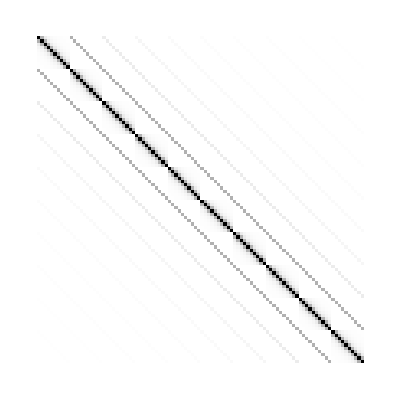

```mathematica
cartK//ArrayPlot
```

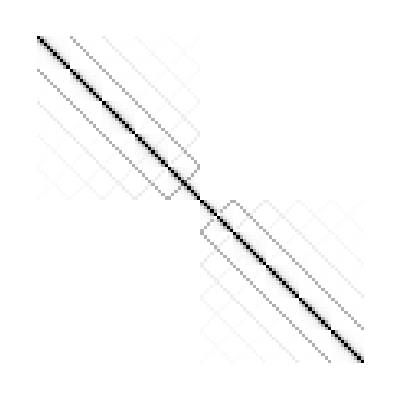

```mathematica
k//ArrayPlot
```

### Matrix Builder

```mathematica
nx=3;
ny=2;
n=nx*ny;
symmT=
Array[
Which[
#==#2&&#≤n/2,1/(√2),
#==#2&&#≥n/2,-1/(√2),
#2==n-#+1,1/(√2),
True,0
]&,
{n,n}
];
tbase=
Array[t,{n,n}];
tks=
Array[
Indexed[δ,{y,##}]Indexed[t,{x,##}]+
Indexed[δ,{x,##}]Indexed[t,{y,##}]&,
{n,n}
];
```

#### Expr Builder

```mathematica
noHalfT=√2*symmT;
symmeddy=noHalfT.tks.noHalfT;
```

```mathematica
symmeddy[[;;(n/2),;;1]]//MatrixForm
```

(ty11 δx11+ty16 δx16+ty61 δx61+ty66 δx66+tx11 δy11+tx16 δy16+tx61 δy61+tx66 δy66
ty21 δx21+ty26 δx26+ty51 δx51+ty56 δx56+tx21 δy21+tx26 δy26+tx51 δy51+tx56 δy56
ty31 δx31+ty36 δx36+ty41 δx41+ty46 δx46+tx31 δy31+tx36 δy36+tx41 δy41+tx46 δy46)

```mathematica
symmeddy[[-(n/2);;-1,-(n/2);;-1]]//MatrixForm
```

(ty33 δx33-ty34 δx34-ty43 δx43+ty44 δx44+tx33 δy33-tx34 δy34-tx43 δy43+tx44 δy44 | ty32 δx32-ty35 δx35-ty42 δx42+ty45 δx45+tx32 δy32-tx35 δy35-tx42 δy42+tx45 δy45 | ty31 δx31-ty36 δx36-ty41 δx41+ty46 δx46+tx31 δy31-tx36 δy36-tx41 δy41+tx46 δy46
ty23 δx23-ty24 δx24-ty53 δx53+ty54 δx54+tx23 δy23-tx24 δy24-tx53 δy53+tx54 δy54 | ty22 δx22-ty25 δx25-ty52 δx52+ty55 δx55+tx22 δy22-tx25 δy25-tx52 δy52+tx55 δy55 | ty21 δx21-ty26 δx26-ty51 δx51+ty56 δx56+tx21 δy21-tx26 δy26-tx51 δy51+tx56 δy56
ty13 δx13-ty14 δx14-ty63 δx63+ty64 δx64+tx13 δy13-tx14 δy14-tx63 δy63+tx64 δy64 | ty12 δx12-ty15 δx15-ty62 δx62+ty65 δx65+tx12 δy12-tx15 δy15-tx62 δy62+tx65 δy65 | ty11 δx11-ty16 δx16-ty61 δx61+ty66 δx66+tx11 δy11-tx16 δy16-tx61 δy61+tx66 δy66)

```mathematica
symmeddy[[1,1]]
```

```mathematica
tx[1,1]+tx[1,9]+tx[9,1]+tx[9,9]+ty[1,1]+ty[1,9]+ty[9,1]+ty[9,9]
```

```mathematica
symmeddy[[1,2]]
```

tx[1,2]+tx[1,8]+tx[9,2]+tx[9,8]+ty[1,2]+ty[1,8]+ty[9,2]+ty[9,8]

```mathematica
symmeddy[[2,1]]
```

tx[2,1]+tx[2,9]+tx[8,1]+tx[8,9]+ty[2,1]+ty[2,9]+ty[8,1]+ty[8,9]

```mathematica
symmExprCellPrint[expr_]:=
CellPrint[
Cell[
BoxData@
StringReplace[
ToBoxes[SequenceForm@InputForm@expr][[1,1,1]],
{
","->",
",
"If["->"
If["
}
],
"Input"
]
]
```

```mathematica
tcm[{i_,j_},m_,d_]:=
1/Sqrt[2]*(
ℏ^2(-1)^(i-j)
)/(2m d^2)*(
	If[i==j,
π^2/3,
2/(i-j)^2
]
);
```

```mathematica
Set[
symmFormPlus,
(
symmeddy[[1,1]]//.{
tx[{i:1|n,j_}]:>
tx[{Switch[i,1,ix,n,(Np-ix+1)],j}],
tx[{i_,j:1|n}]:>
tx[{i,Switch[j,1,jx,n,(Np-jx+1)]}],
ty[{i:1|n,j_}]:>
ty[{Switch[i,1,iy,n,(Np-iy+1)],j}],
ty[{i_,j:1|n}]:>
ty[{i,Switch[j,1,jy,n,(Np-jy+1)]}]
}
)/.{
tx[{a_,b_}]:>
With[{res=tcm[{a,b},mx,dx]},
If[iy==jy,
0,
res
]
],
ty[{a_,b_}]:>
With[{res=tcm[{a,b},my,dy]},
If[ix==jx,
0,
res
]
]
}
]//Simplify//symmExprCellPrint
```

Simplify::time: Time spent on a transformation exceeded 300. seconds, and the transformation was aborted. Increasing the value of TimeConstraint option may improve the result of simplification.

```mathematica
Set[
symmFormMinus,
(
symmeddy[[-1,-1]]//.{
tx[{i:1|n,j_}]:>
tx[{Switch[i,1,ix,n,(Np-ix+1)],j}],
tx[{i_,j:1|n}]:>
tx[{i,Switch[j,1,jx,n,(Np-jx+1)]}],
ty[{i:1|n,j_}]:>
ty[{Switch[i,1,iy,n,(Np-iy+1)],j}],
ty[{i_,j:1|n}]:>
ty[{i,Switch[j,1,jy,n,(Np-jy+1)]}]
}
)/.{
tx[{a_,b_}]:>
With[{res=tcm[{a,b},mx,dx]},
If[iy==jy,
0,
res
]
],
ty[{a_,b_}]:>
With[{res=tcm[{a,b},my,dy]},
If[ix==jx,
0,
res
]
]
}
]//Simplify//symmExprCellPrint
```

Simplify::time: Time spent on a transformation exceeded 300. seconds, and the transformation was aborted. Increasing the value of TimeConstraint option may improve the result of simplification.

```mathematica
(
If[ix == jx,
 0,
 ((-1)^(iy - jy)*ℏ^2*
If[iy == jy,
 Pi^2/3,
 2/(iy - jy)^2])/(2*Sqrt[2]*dy^2*my)] - 
If[ix == jx,
 0,
 ((-1)^(-1 + iy + jy - Np)*ℏ^2*
If[iy == 1 - jy + Np,
 Pi^2/3,
 2/(iy - (1 - jy + Np))^2])/(2*Sqrt[2]*dy^2*my)] - 
If[ix == jx,
 0,
 ((-1)^(1 - iy - jy + Np)*ℏ^2*
If[1 - iy + Np == jy,
 Pi^2/3,
 2/((1 - iy + Np) - jy)^2])/(2*Sqrt[2]*dy^2*my)] + 
If[ix == jx,
 0,
 ((-1)^(-iy + jy)*ℏ^2*
If[1 - iy + Np == 1 - jy + Np,
 Pi^2/3,
 2/((1 - iy + Np) - (1 - jy + Np))^2])/(2*Sqrt[2]*dy^2*my)] + 
If[iy == jy,
 0,
 ((-1)^(ix - jx)*ℏ^2*
If[ix == jx,
 Pi^2/3,
 2/(ix - jx)^2])/(2*Sqrt[2]*dx^2*mx)] - 
If[iy == jy,
 0,
 ((-1)^(-1 + ix + jx - Np)*ℏ^2*
If[ix == 1 - jx + Np,
 Pi^2/3,
 2/(ix - (1 - jx + Np))^2])/(2*Sqrt[2]*dx^2*mx)] - 
If[iy == jy,
 0,
 ((-1)^(1 - ix - jx + Np)*ℏ^2*
If[1 - ix + Np == jx,
 Pi^2/3,
 2/((1 - ix + Np) - jx)^2])/(2*Sqrt[2]*dx^2*mx)] + 
If[iy == jy,
 0,
 ((-1)^(-ix + jx)*ℏ^2*
If[1 - ix + Np == 1 - jx + Np,
 Pi^2/3,
 2/((1 - ix + Np) - (1 - jx + Np))^2])/(2*Sqrt[2]*dx^2*mx)])/2
```

```mathematica
<<CompiledFunctionTools`
```

```mathematica
symmeddy[[2,3]]
```

```mathematica
symmeddy[[;;(n^2)/2,;;n^2/2]]//Simplify//MatrixForm
```

```mathematica
symmeddy[[1+(n^2)/2;;,1+(n^2)/2;;]]//Simplify//MatrixForm
```

```mathematica
symmeddy//Simplify//MatrixForm
```

```mathematica
symmeddy[[1,7]]//Simplify
```

1/2 (tx15+tx62+ty12+ty15+ty62+ty65)

### Test

```mathematica
Needs["ChemTools`DVR`"]
```

```mathematica
ChemDVRReload["Cartesian2DC2DVR"];
```

```mathematica
obj=ChemDVRClass["Cartesian2DC2DVR"][{10,20}]
```

ChemDVRObject[…]

#### Misc Tests

```mathematica
obj["PotentialEnergy"]
```

```mathematica
{solns, grid, other}=obj[];
```

```mathematica
ListPlot3D[
Partition[#, 20],
PlotRange->All
]&/@Take[solns[[2]], 20]
```

```mathematica
grid[[1]]//Length
```

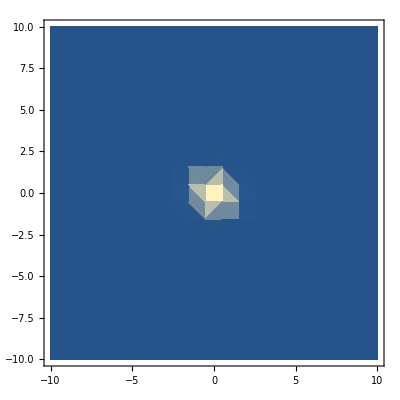
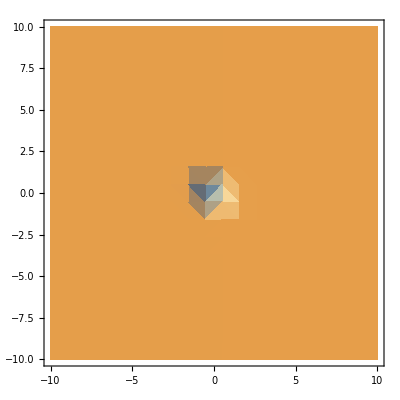
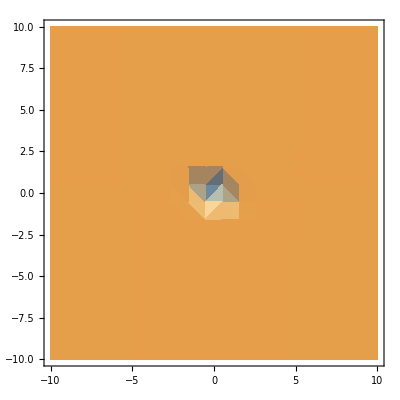
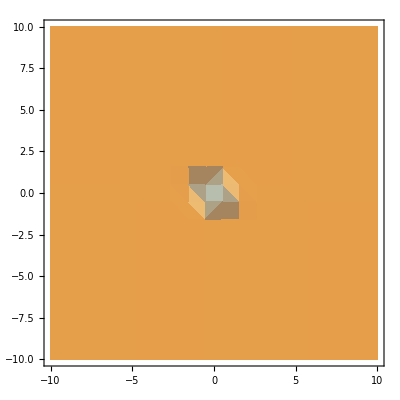
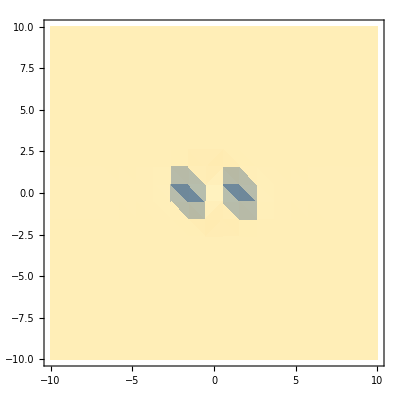
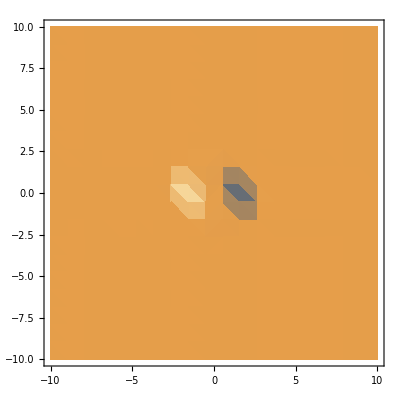
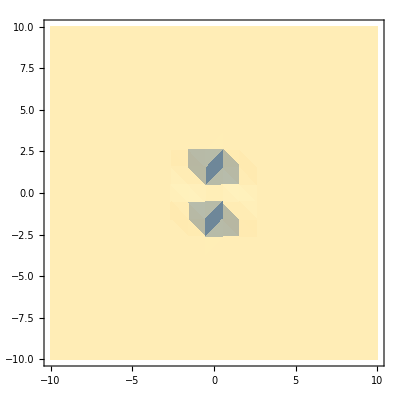
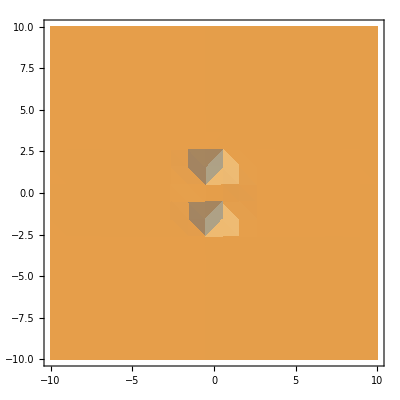
1 | -Graphics- | 2 | -Graphics- | 3 | -Graphics- | 4 | -Graphics-
5 | -Graphics- | 6 | -Graphics- | 7 | -Graphics- | 8 | -Graphics-
9 | -Graphics- | 10 | -Graphics- | 11 | -Graphics- | 12 | -Graphics-
13 | -Graphics- | 14 | -Graphics- | 15 | -Graphics- | 16 | -Graphics-

```mathematica
MapIndexed[
{
#2[[1]],
ListDensityPlot[
MapThread[
Append,
{
Flatten[grid,1],
#
}
],
PlotRange->All
]
}&,
Take[solns[[2]],16]
]//Partition[#, 4]&//Map[Flatten]//Grid
```

```mathematica
og=obj[Return->"Grid"];
ok=obj[Return->"KineticEnergy"];
op=obj[Return->"PotentialEnergy"];
```

```mathematica
wf=obj[Return->"Wavefunctions"];
```

```mathematica
wf[[2]]
```

```mathematica
og
```

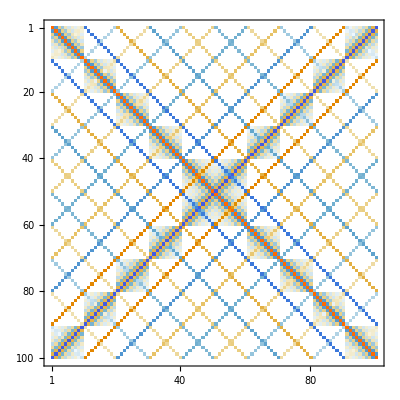

```mathematica
ok[[2]]//MatrixPlot
```

```mathematica
Eigenvalues[ok+op
```

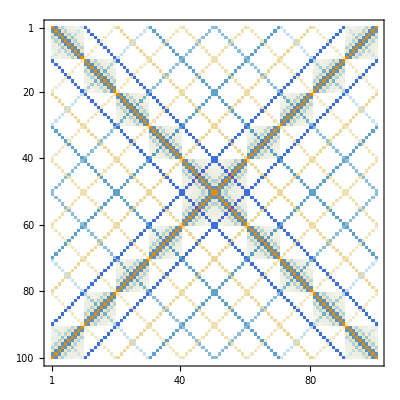

```mathematica
ok[[1]]//MatrixPlot
```

#### Full

```mathematica
ChemDVROptions[obj, "View"]
```

```mathematica
obj[Function->(#[[1]]^2/10-((Abs@#[[2]]-6)^2)/100&)]
```

## Compilable Interpolation

```mathematica
Needs["ChemTools`DVR`"]
```

```mathematica
ChemDVRReload["Cartesian2DC2DVR"];
```

```mathematica
dvr=ChemDVRClass["Cartesian2DC2DVR"][];
```

```mathematica
pot=Import[FileNameJoin@{NotebookDirectory[],"2d_pot.dat"},"TSV"];
potGrid=DeleteCases[pot,{}][[2;;,{1,2,5}]];
```

```mathematica
potInterp=Interpolation[potGrid];
```

```mathematica
CoordinateBounds[potGrid[[All, ;;2]]][[1]];
```

```mathematica
gridNew=
Join[(*
RandomSample[potGrid[[All,;; 2]], Floor[Length[potGrid]/2]],*)
RandomReal[CoordinateBounds[potGrid[[All, ;;2]]][[1]], {Length[potGrid], 2}]
];
```

```mathematica
newGrid=Thread[{gridNew, potInterp@@@gridNew}];
```

```mathematica
ListDensityPlot[Evaluate[Map[Flatten]@newGrid]]
```

```mathematica
newGridSort=SortBy[newGrid, First];
```

```mathematica
pwf=
Piecewise[
Map[
{InterpolatingPolynomial[#,{x, y}],x<#[[3,1, 1]]}&,
Most[#]
],
InterpolatingPolynomial[Last@#,{x,y}]
]&@Partition[newGridSort,4,1];
```

```mathematica
(*pwfWhich=
Replace[
pwf,
Verbatim[Piecewise][l_, f_]:>
Which@@
Replace[Append[l, f],
{
 {v_, c_}:>Sequence@@{c, v}, 
e_:>Sequence@@{True, e}
},
1]
];*)
```

```mathematica
compPF=
Compile[{{x, _Real}, {y, _Real}},
Evaluate[pwf],
"RuntimeOptions"->{"EvaluateSymbolically"->False},
RuntimeAttributes->{Listable},
CompilationOptions->{"InlineExternalDefinitions"->True}
];
```

```mathematica
DensityPlot[compPF[x, y], {x, .5 ,3.5}, {y, .5, 3.5}]
```

```mathematica
compPF[1, 2]
```

3099.73